Coordinate system

The earth is represented as the S_2unit sphere immerged in ℝ^3. Coordinates are {θ, ϕ}, where θ ∈ [0, 2 ℼ) spans longitudes eastwardly and ϕ ∈ [-ℼ/2, +ℼ/2 ] spans latitudes from south to north pole. The immersion follows the standard application:

				[0, 2 ℼ)	 × [-ℼ/2, +ℼ/2 ]	⟶	S_2 ⊂ ℝ^3
					{θ, ϕ}		⟶	X_(θ,ϕ)= (cos(θ)cos(ϕ)
sin(θ)cos(ϕ)
sin(ϕ))
				
As computations are perfomed in degrees, minutes and seconds, the usual scaling α ⟶ ℼ/180α is introduced, thus providing the following expression:

```mathematica
X[{θ_,ϕ_}]:={Cos[π/180 θ]Cos[π/180 ϕ],Sin[π/180 θ]Cos[π/180 ϕ],Sin[π/180 ϕ]};
```

Orthodromy

An orthodromy is a shortest route linking two locations on a geometrical surface, according to the intrisic metric of that surface. Orthodromies are usually computed following a extremal principle delivering a second order differential equation, whose solution is the orthodromy. On the sphere, othodromies are constructed as follow: consider two locations {θ_1,ϕ_1} and  {θ_2,ϕ_2}on the sphere. Together with the center of the sphere,  X_c ={0,0,0}, the points X_(θ_1,ϕ_1)and X_(θ_2,ϕ_2)define a plane whose intersection with the sphere is a circle on the sphere, indeed the orthodromy. Of course, starting from{θ_1,ϕ_1}, {θ_2,ϕ_2} can be reached by travelling on the circle into two, shorter or longer, directions.

Historically, orthodromies on earth are called “arcs of great circle”, whereas the arc is indeed the short path.

Making use of the scalar product between two vectors A and B: A · B =  ‖A‖ ‖B‖ Cos[∢(A, B)], the distance on the sphere between two locations {θ_1,ϕ_1} and  {θ_2,ϕ_2}  is provided by the module Ortho computing ArcCos[X_(θ_1,ϕ_1). X_(θ_2,ϕ_2)] (remember that the radius of our sphere is unity). Making use of // FullSimplify provides the following module, delivering the distance between two locations, expressed in nautical miles.

```mathematica
Ortho[{x1_,y1_},{x2_,y2_}]:=Module[{θ1,ϕ1,θ2,ϕ2},
{θ1,ϕ1,θ2,ϕ2}=π/180{x1,y1,x2,y2};
N[(360  60)/(2π) ArcCos[Cos[θ1-θ2] Cos[ϕ1] Cos[ϕ2]+Sin[ϕ1] Sin[ϕ2]]]
];
```

Why nautical miles?

On earth, one Nautical Mile is the distance separating two locations {θ_1,ϕ_1} and  {θ_2,ϕ_2}  making with the centre of earth X_c an angle ∢ (X_(θ_1,ϕ_1), X_c , X_(θ_2,ϕ_2)) that equals to one minute of degree.
This explains the coefficient (360 60)/(2 ℼ)in the expression of Ortho. By that way, our computations are performed without any reference to the actual radius of earth, or of any planet on which a regatta would be organized. Furthemore, computing speed in knots - nautical miles per hour - makes us only dependent on the angular rotation of the planet, one full rotation of 2 ℼ in 24 hours. This definition justifies the way the module Ortho is concieved. This system is valid on any other planet or spherical body. Expressed in our usual unit system, the values of the nautical mile and the knot would simply be different. And of course, I almost forgot it, on earth 1 Nautical Mile = 1.852 km, 1 Knot = 0.514 m/s.

Constructing an Array of Nodes

The following module Graphe enables the construction of a grid of nodes, indeed the array of nodes onto which a decision tree will be afterwards computed. All elements are given in {θ, ϕ} = {longitudes, latitudes}, in this order. Two anchors are provided as input, AncrDep for Anchor at Dearture and AncrArr for Anchor at Arrival. Represented as green dots on following figure 1, they enable the positionning of the grid and are  provided as parameters {θ_1,ϕ_1} and {θ_2,ϕ_2} at the call of the module Graphe. The number of nodes in the array is given by {m, n}. The number of steps from departure to arrival is specifiend by m, in that case 20, the number of options by n, running between -n and +n, in that case 21 options.  The parameter ρ specifies the ratio of the distances between two steps and two options, The euclidian distance between Departure and Arrival is computed as e=((θ_2-θ_1)^2+(ϕ_2-ϕ_1)^2)^(1/2). The gridsteps are given by e/m and  ρ e/m. As the graph can be rotated in any fashion, the rotation angle τ is provided by Cos[τ]=(θ_2-θ_1)/e and Sin[τ]=(ϕ_2-ϕ_1)/e,
thus delivering the rotation matrix M_[τ] =(Cos[τ] | -Sin[τ]
Sin[τ] | Cos[τ]). The construction of the array of nodes is finally  provided by: (Cos[τ] | -Sin[τ]
Sin[τ] | Cos[τ])·(e/m i
 ρ e/m j)+(θ_1
ϕ_1), as expressed in the module Graphe.

```mathematica
Graphe[{θ1_,ϕ1_},{θ2_,ϕ2_}]:=Module [{ρ,e,c,s,M,m,n},
ρ=0.3;
{m,n}={5,2};
e=((θ2-θ1)^2+(ϕ2-ϕ1)^2)^(1/2);
{c,s}={(θ2-θ1)/e,(ϕ2-ϕ1)/e};
M:=({{c, -s}, {+s, c}});
Table[N[M.{e/m i,ρ e/m j}+{θ1,ϕ1}],{i,0,m},{j,-n,n}]];
```

Example

Figure 1 shows the array of nodes constructed with the module Graphe with a Departure anchor located in Northeast Switzerland, an Arrival Anchor in South Pacific. Achors AncreDep and AncreArr are {longitudes, latitudes} defined in degrees in the two first instructions, they are pictured in green in figure 1. The matrix Loc contains the coordinates {θ, ϕ} of the nodes in the array. It is constructed by the call Loc = Graphe[AncreDep, AncreArr]. The dimension of Loc is then computed with the instruction {Maxi, Maxj, Coord}=Dimensions[Loc]. Loc, Maxi and Maxi will be used later by the module DynProgr while performing the dynamical programming.

```mathematica
AncreDep={8.05,47.3};
AncreArr= {226.88,-47.22};
Loc = Graphe[AncreDep,AncreArr];
{Maxi,Maxj,Coord}=Dimensions[Loc];
```

Following graphical instructions draw figure 1.

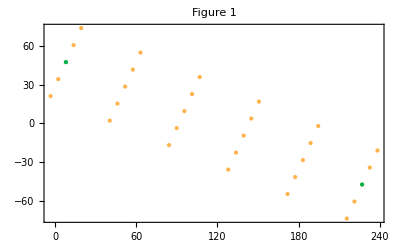

```mathematica
GD=Graphics[{RGBColor[0,0.7,0.3], Point[AncreDep]}];
GA=Graphics[{RGBColor[0,0.7,0.3], Point[AncreArr]}];
G1=Table[Graphics[{RGBColor[1,0.7,0.3], Point[Loc[[i,j]]]}],{i,1,Maxi},{j,1,Maxj}];
Show[G1,GD,GA,Frame-> True, PlotLabel-> "Figure 1"]
```

Dynamical Programming, a first glance

Dynamical Programming covers a set of methodolgies aimed at optimizing sequential decisions. Belonging to the realm of applied mathematics, it consist in defining a sequence of steps at which decisions have to be settled, taking into account progress done so far, as well as future opportunities. Invented by the end of the second World War, Dynamical Programming has blossomed into a vast array of fields, from logistics to finance.

In our application - sailing -, the objective is obvious: defining the course of a sailing boat enabling the shortest time from a departure to an arrival point. To that purpose, geographical specifications, as well as winds ahead on water surfaces and their interaction with the sailing boat have to be integrated into a comprehensive decision scheme.

Getting started

Let we start smoothly and consider firstly a vehicle moving on earth's surface at constant speed. It is for example required to travel from the Departure to the Arrival Achor in the previous diagramme. The sequencing is provided by the slicing of the array on figure 1, from the northwest to the southeast side of the array. Starting with a very simple formulation that will be progressively refined, one defines:
	
	Δt_i, 	i = 1 ... m, is the time requiered to travel from the slice i-1 to the slice i, with i = 0 corresponding to the first 		slice, to which Departure Anchor belongs, and i = m for the last slice, to which Arrival Anchor belongs.
	
	D_(i,)	i = 0 ... m the time at which the slice i is crossed
		T_(i,) i = 0 is the departure time,
		T_(i,) i = m is the arrival time	
		
Our optimal programme can thus be defined as “minimize the travel duration D_m from slice 0 to slice m”:
	
	 D_m = Min_(i=1)^m[  ∑_(i=1)^m Δt_i]. 							(1)
Let we consider an intermediary step I and evaluate D_I = Min_(i=1)^I[ ∑_(i=1)^I Δt_i]. It can be rewritten:
 D_I = Min_(i=1)^I [Δt_I+  ∑_(i=1)^(I-1) Δt_i] =    Min^I[Δt_I+Min_(i=1)^(I-1)[  ∑_(i=1)^(I-1) Δt_i]] =  Min^I[Δt_I+ D_(I-1)]. Our initial question emerges anew in the the penultimate expression at step I-1. Thus, equating the first and final expressions provides a recursive formulation of the problem. An initial value has to be specified, provided by D_0=D_(i=0) = departure time, giving:		
	 D_I =  Min^I[Δt_I+ D_(I-1)]; 	 D_0: departure time.					(2)	
			
This derivation results from a profound optimization principle, assessing that a strategy is optimal if and only if all its sub-strategies are optimal. Of course, such a flat rate formulation conceals the decision process.

Deciding consist here in choosing:

	for each node j of the slice I-1, towards which node k of the next slice I the boat should sail, 
		
		or equivalently,
		
	for each node k of the slice I from which node j of the previous slice I-1 the boat should have sailed.

Introducing the latter condition in the previous expression for D_I gives (with standard {i, j} typography for representing nodes in graph theory):
	
	 D_{I,k} =   Min_(j=-n)^(j=n)[Δt_{I-1, j}^{I, k}+ D_{I-1,j}]; 	 D_0: departure time.		(3)

The node j^*belonging to the slice I-1 and satisfying the above minimum is the decision taken in the slice I for the node k. It is expressed as:
	
	D_{I,k} ⟶ j^* ∈  slice I-1.									(4)
	
The reader will have noticed that the expression D - for Duration - can be easly traded for D, for Decision.  Adopting this convention, D_I in expression (2) is the set of all the decisions taken in the slice I, for each node k of that slice:

	D_I ⟶ {(j^*)_-n ...   (j^*)_k ...  (j^*)_n }  ⊂  slice I-1.					(5)
	
To be remembered, the number of steps from departure to arrival is specifiend by m, the number of options by n, running between -n and +n, in that case 21 options. 

A further refinement has to be introduced. For a node located on one side of the array, as for example in the i-th slice on the left side of the array, node {i,-n}, the algorithm could choose the node {i-1,+n} as its predecessor, thus forcing a lateral crossing through the array, indeed an unfortunate situation. A control mechanism, defining for each node {i, k} in the i slice which are the {i-1, k} nodes that can be addressed in the i-1 slice, is introduced. It is controlled by the Spread parameter whose modus operandi is defined as:

	D_{I,k} ⟶ j^*  with |j^* - k| ≤ Spread;  j^* ∈  slice I-1.					(6)

A neighborhood is thus defined in slice i-1 for each node k in slice i. Other nodes {i-1, j^*} not satisfying the requirement |j^* - k| ≤ Spread are simply disregarded during the selection process. In a further version of the algrorithm, the spread parameter will enable us to cope with the geography of the lake, when the array of nodes may reach outside of its shore. Everything said above is encapsulated in the following Dynamical Programming Module, that deserves to be yet described.

The Module DynProgr

DynProgr performs the dynamical programming and delivers the matrix Decision pictured below. This matrix describes all relevant parameters with each of its elements representing one node of the decision tree. It has dimensions Maxi, Maxj, the dimension of the table of coordinates Loc delivered by the module Graphe previously presented. DynProgr uses an internal module ProgrDyn that will be discussed below.

DynProgr starts after the comment line (* DynProgr starts here ;*). In the first instruction, a matrice Grph is generated with all its elements initialized at  (0
1000000). The 0 is an empty location that will be used later, the 1’000’000 is a navigation duration, expressed in hours and initializated at a high value: 1 million hours. The starting node, given as input of the module: Start_, is determined in the second instruction: The locator is set at one, the departure time at 0 hours. One notices that the starting node is not necessarily the Departure Anchor, it can be set on any node of the first row. The third instruction executes the dynamical programming: it computes expression (5) from the second slice (indexed r) up to the last one: Do[ ProgrDyn[r], {r, 2, Maxi}]. The transposition finally provides the matrix Decision exhibited below.

ProgrDyn, the internal module, receives as input parameter the current slice and do exactly three things:

1. Instruction Etabli: computes for each node {slice, k}  the table of arrival times at that node {slice, k} from each node {slice-1, j}, using the arrival time at node {slice-1, j} given by Grph[[slice-1, j, 2]] and adding Ortho[Loc[[slice-1, j]],Loc[[slice, k]]].  Loc[[slice-1, j]] and Loc[[slice, k]] are {θ, ϕ} of both nodes.

2. Instruction {{Posi}} uses a standard Mathematica command to find the position of a minimum value in the table Etabli, thus giving us (j^*)_k in expression (5).

3. Last instruction computes the spread, as defined in expression (6) and updates the matrix Grph.

This concludes the description of DynProgr.

```mathematica
DynProgr[Start_]:=Module[{Grph,ProgrDyn},

ProgrDyn[slice_]:=Module[{Spread,Etabli,Posi},
Spread=4;
Do[
	Etabli=Table[Grph[[slice-1,j,2]]+Ortho[Loc[[slice-1,j]],Loc[[slice,k]]],{j,1,Maxj}];
	
	{{Posi}}=Position[Etabli,Min[Etabli]];
	
	If[Abs[k-Posi]≤Spread,Grph[[slice,k]]={{{slice-1,Posi},{slice,k}},Min[Etabli]}],{k,1,Maxj}]

	]; (* end ProgrDyn *)

(* DynProgr starts here ;*)

Grph=Table[{0,10^6},{i,1,Maxi},{j,1,Maxj}];

Grph[[1,Start]]={1,0};

Do[ProgrDyn[r],{r,2,Maxi}];

Transpose[Grph] 

]; (* End Programmation Dynamique *)
```

Finally, each element of the Decision matrix has the following structure:

({{3,4},{4,3}}
8017.32)with ({{previous node},{node}}
time of arrival).

```mathematica
Decision=DynProgr[2];
Dtable=Decision//MatrixForm
```

((0
1000000) | ({{1,2},{2,1}}
2868.47) | ({{2,2},{3,1}}
5578.4) | ({{3,1},{4,1}}
8165.43) | ({{4,1},{5,1}}
10288.8) | ({{5,1},{6,1}}
11837.1)
(1
0) | ({{1,2},{2,2}}
2615.33) | ({{2,2},{3,2}}
5451.38) | ({{3,3},{4,2}}
8195.06) | ({{4,1},{5,2}}
10479.) | ({{5,1},{6,2}}
11881.)
(0
1000000) | ({{1,2},{2,3}}
2534.11) | ({{2,3},{3,3}}
5244.3) | ({{3,4},{4,3}}
8017.32) | ({{4,4},{5,3}}
10665.6) | ({{5,1},{6,3}}
12363.8)
(0
1000000) | ({{1,2},{2,4}}
2603.5) | ({{2,4},{3,4}}
5066.86) | ({{3,5},{4,4}}
7746.41) | ({{4,5},{5,4}}
10443.2) | ({{5,4},{6,4}}
13060.)
(0
1000000) | ({{1,2},{2,5}}
2773.7) | ({{2,5},{3,5}}
4894.73) | ({{3,5},{4,5}}
7480.21) | ({{4,5},{5,5}}
10308.) | ({{5,5},{6,5}}
13105.5))

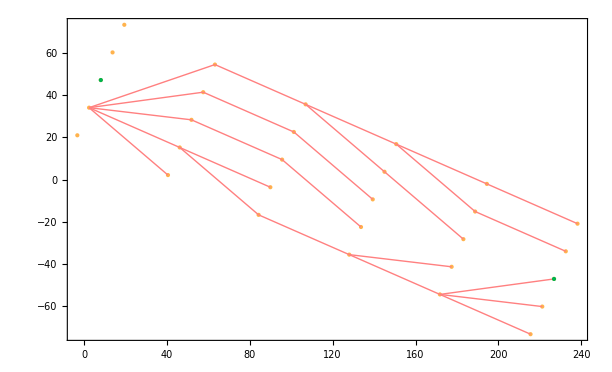

```mathematica
G0=Table[Graphics[{RGBColor[1,0.7,0.3], Point[Loc[[i,j]]]}],{i,1,Maxi},{j,1,Maxj}];
G1=Table[Graphics[{RGBColor[1,0.7,0.3], Point[Loc[[i,j]]]}],{i,1,Maxi},{j,1,Maxj}];
G2=Select[Flatten[Decision,1],(Last[#]<1000000)&&(Last[#]>0.1)&];
DimG2=First[Dimensions[G2]];
G3=Table[First[G2[[i]]],{i,1,DimG2}];
G4=Table[{Loc[[First[G3[[i]]][[1]],First[G3[[i]]][[2]]]],Loc[[Last[G3[[i]]][[1]],Last[G3[[i]]][[2]]]]},{i,1,DimG2}];
G5=Table[Graphics[{RGBColor[1,0.5,0.5],Line[{G4[[i,1]],G4[[i,2]]}]}],{i,1,DimG2}];
Show[G1,G5,GD, GA,Frame-> True]
```

```mathematica
G6=Table[{N[X[G4[[i,1]]]],N[X[G4[[i,2]]]]},{i,1,DimG2}];
G7=Table[Graphics3D[{RGBColor[1,0.5,1],Line[{G6[[i,1]],G6[[i,2]]}]}],{i,1,DimG2}];
Earth=Graphics3D[Sphere[{0,0,0}]];
Show[Earth,G7]
```